Cool idea from here
https://mathematica.stackexchange.com/questions/256942/how-to-extract-different-curves-from-a-mixed-dataset
Worth trying it out

```mathematica
findNewStartingPoint[data_/;Length@data<=2]={0,0};
findNewStartingPoint[data_]:=Module[{hull,first,second,newdata},
hull=MeshCoordinates[ConvexHullMesh[data]];(* this creates the boundaries that encompass the entire mesh*)
first=First@RandomSample[hull,1];(* randomly selects one of the mesh boundaries*)
newdata=Delete[data,Position[N@data,first]]; (* deletes the randomly selected point from the dataset *) 
second=First@Nearest[newdata->{"Index","Element"},first];(* finds the element closest to the one currently set as 'first'*) 
newdata=Delete[newdata,second[[1]]];(* removes the second point as well from the dataset*) 
{{first,second[[2]]},newdata}]; (* outputs the first two elements from the mesh, and the newdata which does not contain them *)

findCurves[pts0_,eps_]:=Module[{curves,currCurve,pts,pnt,direction,dr},
direction=1;
curves={};
{currCurve,pts}=findNewStartingPoint[pts0]; (*pick a boundary point and its nearest neighbour. pts is the remaining dataset.*) 
While[Length@pts>0,dr=currCurve[[-1]]-currCurve[[-2]];(* while the mesh has contents, check the vectorial distance between the last two points*)
pnt=First@Nearest[pts->{"Index","Element","Distance"},currCurve[[-2]]+2 dr]; (*and give the nearest element in our dataset that is just 2 such values away from the last currCurve*) 
If[(pnt[[3]]>eps&&direction==-1)||Length@pts==1,(*Curve completed,start a new one*)
AppendTo[curves,currCurve];
{currCurve,pts}=findNewStartingPoint[pts];
direction=1,

If[pnt[[3]]>eps&&direction==1,(*Continue at the other end*)direction=-1;
currCurve=Reverse@currCurve;,
AppendTo[currCurve,pnt[[2]]]; (*Add point to current curve*)
pts=Delete[pts,pnt[[1]]];]]];
curves];

testdata=SortBy[#,#[[1]]&]&@Flatten[{{#,#/(1+Exp[#/20]//Log)+RandomReal[0.3]}&/@Range[100],{#,10+20/#^0.3+RandomReal[0.3]}&/@Range[100]},1];
```

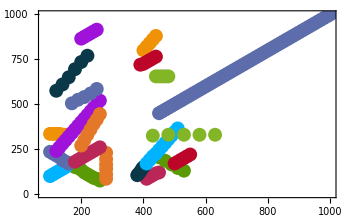

```mathematica
curves=findCurves[N@rdata,5];
newData=DeleteCases[Select[curves,Length@#>=numberOfPoints&],{}];
ListPlot[newData]
```

```mathematica
Union@({Round[a],Round[b,freqPrecisionN]}/.Chop[FindFit[#,a x+b,{a,b},x]&/@newData])
```

{{-1,328},{-1,332},{-1,632},{0,78},{0,318},{0,348},{0,656},{1,-330},{1,-284},{1,0},{1,296},{1,664},{2,-770},{2,-628},{2,0},{2,334},{3,-980},{3,-310}}

```mathematica
Manipulate[Show[{ListPlot[newData],ListPlot[newData[[i]],PlotStyle->pink]}],{i,1,Length@newData,1}]
```